Corso di Laboratorio Computazionale — Corso di Laurea in Matematica — Università di Padova.

Anno Accademico 2019-2020

# Esercizi 1. Grafica e teoria dei numeri

Notebook del gruppo Cammelli Tonanti.
Componenti del gruppo: Francesco Tognetti, Riccardo Cazzin.
Se ci sono stati collaborazioni o aiuti al di fuori del gruppo, dichiararli.
In collaborazione con
Aiutati da

## Esercizio 1.1 (Approssimazione di funzione con il suo sviluppo di Taylor).

### Testo dell’esercizio

Come sono approssimate le funzioni sin(x) e 1/(1+x^2) dai loro polinomi di Taylor di ordine crescente?

### Svolgimento

Dopo un tentativo andato molto molto male di sfruttare lo sviluppo di Taylor scritto da me invece che il built-in, ricomincio.

Il mio obiettivo è di plottare su una griglia dei grafici con passo che aumenta tra le righe di f(x) contro il suo sviluppo in serie di Taylor (in 0), cominciamo dicendo

```mathematica
g[x_]:= 1/(1+x^2)
```

Ora necessito che lo step tra i grafici di una riga sia n quindi automatizzo la creazione delle righe per una funzione generica in un intervallo fissato [-10,10] per limitare le variabili. diamo anche una lunghezza di 4 
fissata alle righe e ricordandoci di quale ordine stiamo facendo il grafico

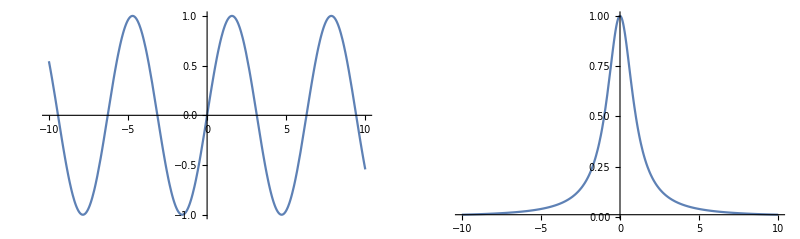

```mathematica
GraphicsRow[{Plot[Sin[x],{x,-10,10}],Plot[g[x],{x,-10,10},PlotRange->Full]}]
```

Possiamo notare che possiamo tenere un PlotRange tra -1 ed 1 senza separarle , per sicurezza facciamo 1.5 valà

```mathematica
Rows[f_,x_,start_,step_]:=Table[Plot[{f[x] , Series[f[x],{x,0,k}]//Normal//Evaluate},{x,-10,10},PlotLabel->k,PlotRange->{-1.5,1.5}],{k,start,start+4 step,step}]
```

La funzione crea una table con il grafico di f(x) e quello della sua serie di Taylor al k-esimo ordine con k che varia, facendo 4 grafici per riga con step fissato

Creiamo una funzione che dia una matrice fatta di “Rows” dove lo step incrementi col numero di righe. ciò crea un problema nel calcolare con cosa far cominciare le righe.

```mathematica
Gridd[f_,x_,n_]:= Table[Rows[f,x,st[k],k],{k,1,n}]
```

lo start della riga 1 è 1, lo start della riga 2 è (1 + 4step(1)+step(1)), lo start della riga 3 è (start della riga 2 + 4step(2)+step(2)) viene in mente di definire ricorsivamente st[k], ricordandoci che step(k) = k per definizione

```mathematica
(*st[k_]:= st[k-1]+ 5k
	st[1]:=1*)
```

Che dà luogo alla formula chiusa:

```mathematica
st[k_]:=1+5/2(-2+k+k^2)
```

Plottiamo e mettiamo in una tabella

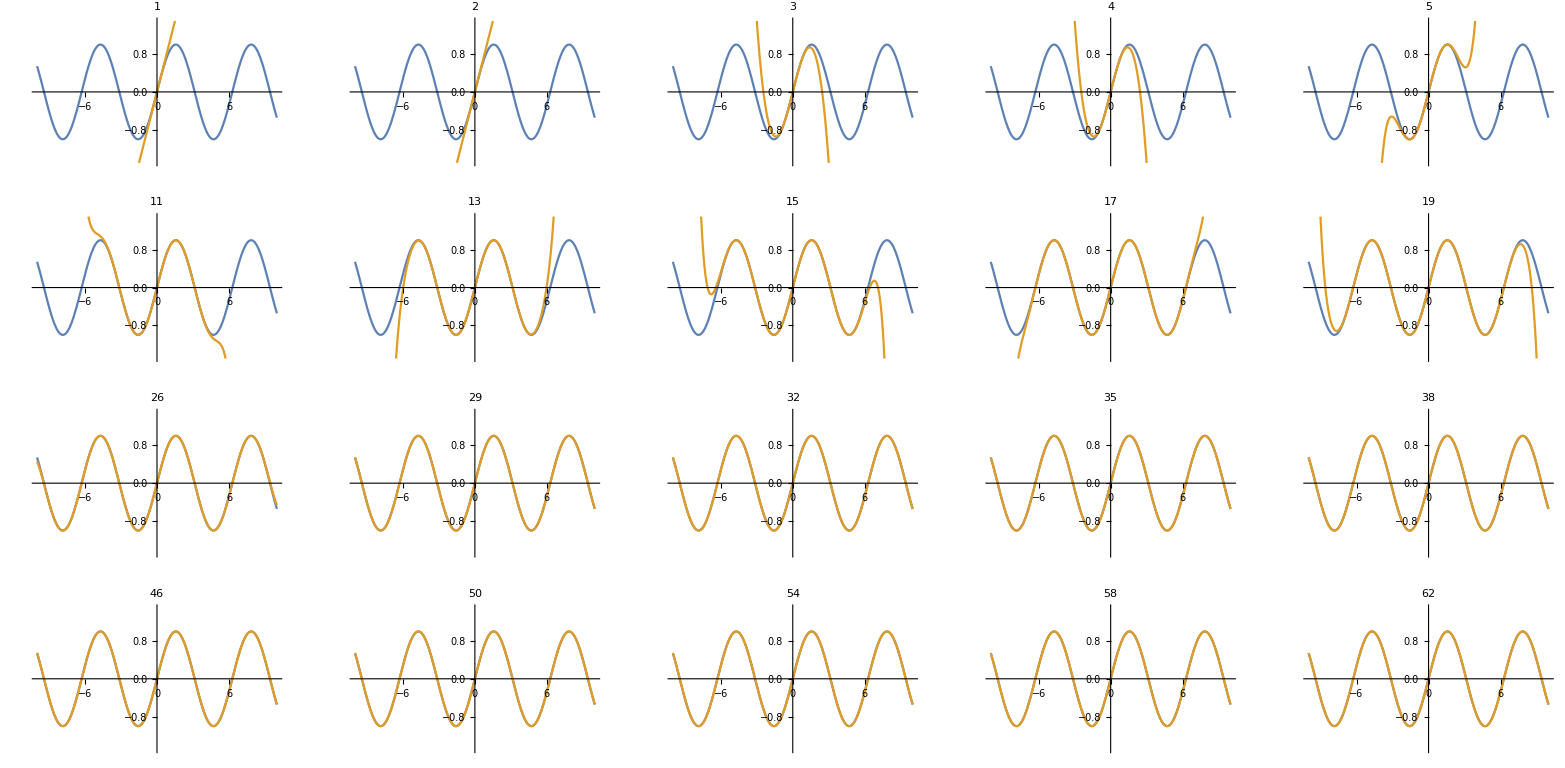

```mathematica
GraphicsGrid[Gridd[Sin,x,4],ImageSize->Full]
```

Proviamo a fare lo stesso con g

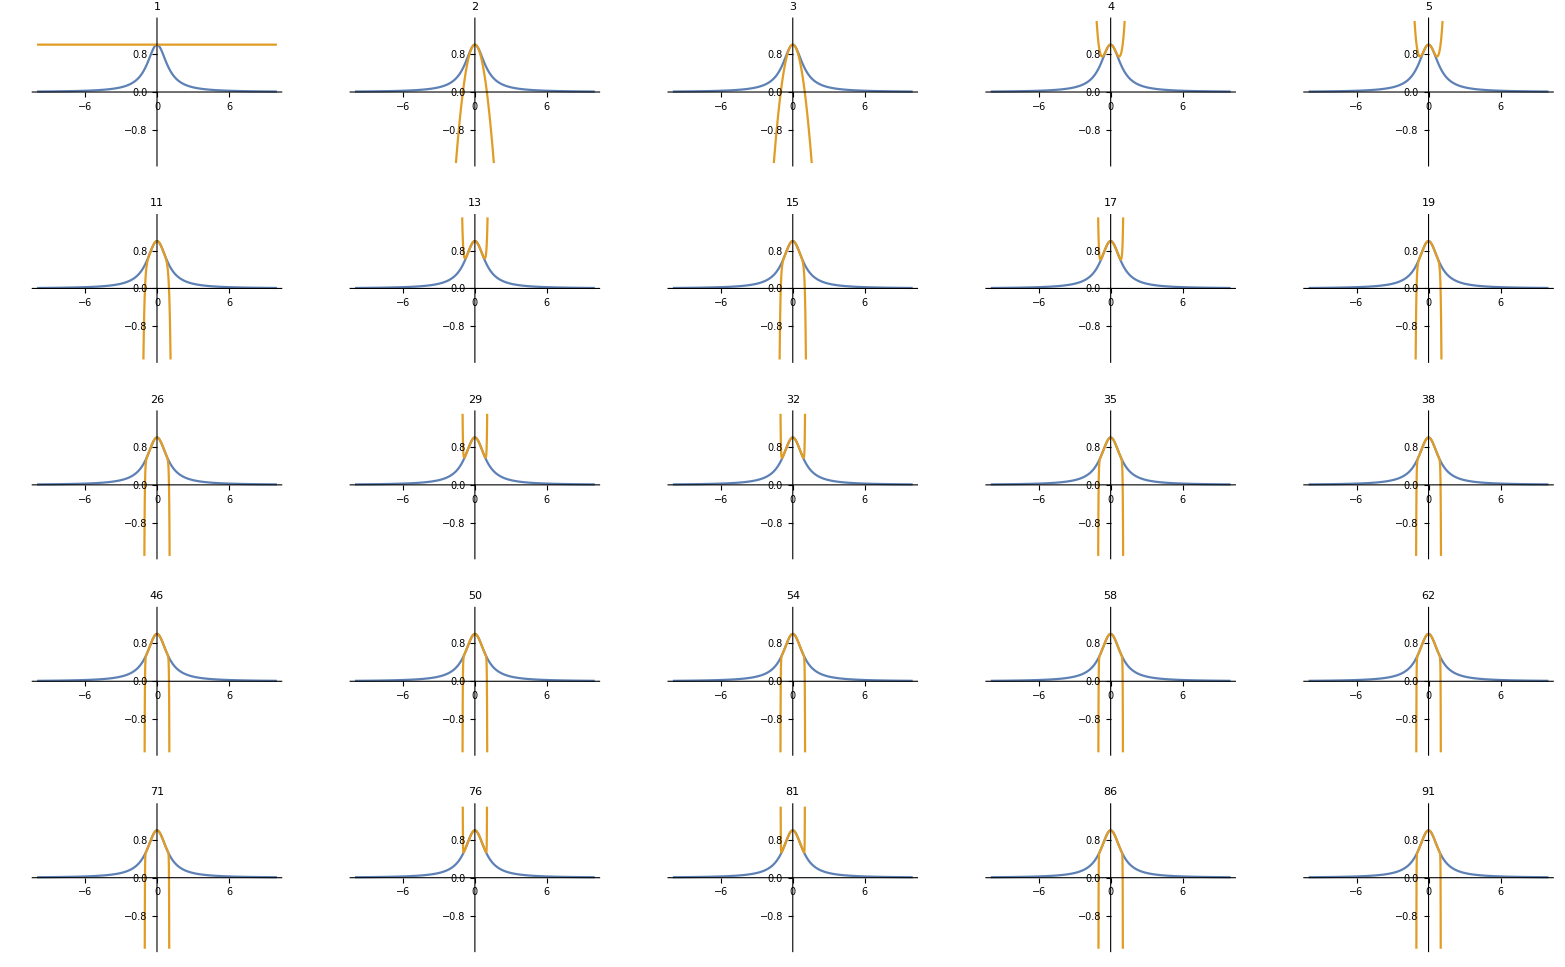

```mathematica
GraphicsGrid[Gridd[g,x,5],ImageSize->Full]
```

Si notano subito spiccate differenze sulla convergenza tra Sin(x) e 1/(1+x^2), la serie di Sin(x), pur essendo entrambe analitiche. 
Lo sviluppo di Sin(x) si “appiccica” alla funzione nell’intervallo [-10,10] in meno di 30 iterazioni, quello di 1/(1+x^2) in 100 non è arrivato a metà
Mi vien da chiedermi quanto sia veloce l’approssimazione, posso provare a farlo plottando n sul il primo x>0 per cui lo sviluppo di ordine n è diverso dalla funzione (entrambe le funzioni hanno simmetrie comode)
scritto matematicamente F(n) = inf(x>0 : |f(x)-s.taylor ord. n f(x)|>0 ), scritto mathematicamente

```mathematica
dst[f_,x_,n_] := Abs[f[x]-Evaluate@Normal[Series[f[x],{x,0,n}]]]
```

si può risolvere numericamente mettendogli un numero “piccolo”>0, forse c’è un metodo migliore

```mathematica
ConvSin=FindRoot[dst[Sin,x,#]==0.01,{x,#-2}]&
```

FindRoot[dst[Sin,x,#1]==0.01,{x,#1-2}]&

```mathematica
Convg=FindRoot[dst[g,x,#]==0.01,{x,#/55}]&
```

FindRoot[dst[g,x,#1]==0.01,{x,#1/55}]&

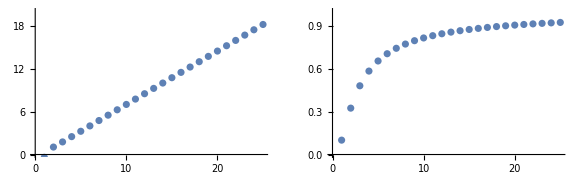

```mathematica
GraphicsRow [{ListPlot[x/.ConvSin/@Range[1,50,2],PlotRange->{0,20}],ListPlot[x/.Convg/@Range[1,50,2],PlotRange->{0,1}]},ImageSize->Large]
```

Sembra una convergenza lineare la prima e logaritmica la seconda.
possiamo vedere come nel medesimo numero di passi il primo sviluppo di Taylor stia “incollato” alla funzione fino a circa x = 20, il secondo circa a x = 1

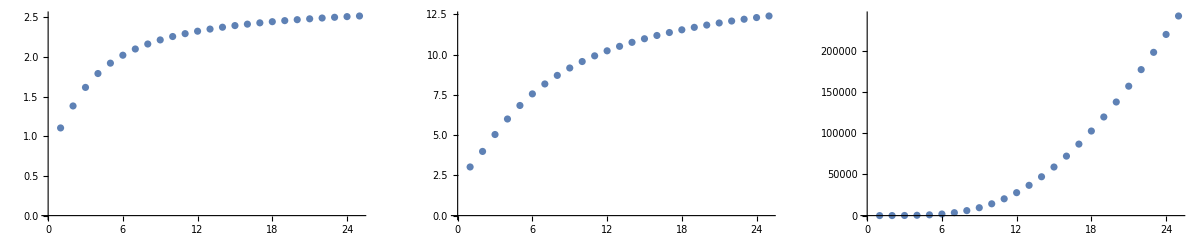

```mathematica
GraphicsRow[{ListPlot[Exp[x/.Convg/@Range[1,50,2]]],ListPlot[Exp@Exp[x/.Convg/@Range[1,50,2]]],ListPlot[Exp@Exp@Exp[x/.Convg/@Range[1,50,2]]]},ImageSize->Full]
```

Tuttavia se plottiamo e^(f(x)) è concava (=> sublineare), così come e^(e^(f(x))), tuttavia e^(e^(e^(f(x))))diventa convessa (=> superlineare), credo si può concludere che la convergenza dell’approssimazione di taylor di 1/(1+x^2) alla funzione sia compresa tra log(log(x)) e log(log(log(x)))

## Esercizio 1.2 (Algebra & Coreografie).

#### Testo dell’esercizio:

Le tre radici del polinomio x^3+b x+c dipendono dai coefficienti b e c e sono genericamente complesse (e distinte, ma per speciali valori di b e c una o tutte possono essere reali e due o tutte possono coincidere).
Per ogni scelta di b e c, le radici sono dunque 3 (o 2 o 1) punti nel piano complesso. 
Se si fa muovere il punto (b,c)ϵR^2 lungo una curva Γ in ℝ^2, le radici si muovono lungo tre curve (che possono avere delle intersezioni) nel piano complesso ℂ.
Si chiede di generare un filmato che mostra, affiancati, il moto del punto (b,c) ϵ  ℝ^2 lungo una curva e il corrispondente moto (o `danza’) delle radici in  ℂ.

#### Svolgimento:

Allora, cominciamo dando un nome al nostro polinomio, equivalentemente assegnando una funzione che manda la terna (b,c,x) nel polinomio di terzo grado sopra

```mathematica
P[b_,c_,x_]:= x^3+b x + c
```

```mathematica
Rads[a_,b_]:= x/.NSolve[P[a,b,x]]
```

Una funzione che dati 2 parametri restituisca le radici

```mathematica
C2R2[a_,b_,k_]:= {Re[Rads[a,b][[k]]],Im[Rads[a,b]][[k]]}
```

```mathematica
PointsRange[a_,b_,range_]:= Graphics[{PointSize[0.02],Red,Point[C2R2[a,b,1]],Green,Point[C2R2[a,b,2]],Blue,Point[C2R2[a,b,3]]},
							PlotRange->{{-range,range},{-range,range}},Axes->True,Ticks->None]
```

Ed una che dati i 2 parametri restituisca i punti come oggetto “Graphics”

```mathematica
Dance[t_,a_,b_,γ1_,γ2_]:= GraphicsRow[{Show[
								{ParametricPlot[{γ1[θ],γ2[θ]},{θ,a,b}],
								Graphics[{Purple,PointSize[0.02],Point[{γ1[t],γ2[t]}]}]}
									],
								Show[{
								Points[γ1[t],γ2[t]],
								ListLinePlot[Table[C2R2[γ1[τ],γ2[τ],1],{τ,a,t,0.05}],PlotStyle->Red],
								ListLinePlot[Table[C2R2[γ1[τ],γ2[τ],2],{τ,a,t,0.05}],PlotStyle->Green],
								ListLinePlot[Table[C2R2[γ1[τ],γ2[τ],3],{τ,a,t,0.05}],PlotStyle->Blue]
								}]
							}]
```

Una funzione che crea 2 grafici, uno con un punto che si muove sul supporto della curva ed uno con le 3 radici e la “traccia” che lasciano

Nota, ho utilizzato ListLinePlot, avevo fatto un tentativo con ListCurvePathPlot ma in termini di tempi di rendering è decisamente più efficace l’ interpolazione lineare della curva (e graficamente ha la stessa resa)

```mathematica
γ1[t_]:=Cos[t]
γ2[t_] := Sin[t]
Points[a_,b_]:= PointsRange[a,b,1.5]
```

Definiamo le componenti di una curva parametrizzata

```mathematica
Manipulate[Dance[t,0,2π,γ1,γ2],{t,0,2π}]
```

Il Manipulate è lento ma dà una comoda Preview di come sarà l’animazione poi

```mathematica
frames = Table[Dance[t,0,2π,γ1,γ2],{t,0,2π,0.05}];
```

$Aborted

```mathematica
Export["dance.gif",frames,ImageSize->Large]
```

### Extra (Generalizzazione a curve in ℝ^3) :

Viene naturale porsi il medesimo problema sul polinomio x^3+ax^2+bx+c con a,b,c che variano lungo una curva in R^3
Gli step sono i medesimi:

```mathematica
P[a_,b_,c_,x_]:= x^3+a x^2+b x + c
```

```mathematica
Rads[a_,b_,c_]:= x/.NSolve[P[a,b,c,x]]
```

```mathematica
C2R2[a_,b_,c_,k_]:= {Re[Rads[a,b,c][[k]]],Im[Rads[a,b,c]][[k]]}
```

```mathematica
PointsRange[a_,b_,c_,range_]:= Graphics[{PointSize[0.02],
														Red,Point[C2R2[a,b,c,1]],
														Green,Point[C2R2[a,b,c,2]],
														Blue,Point[C2R2[a,b,c,3]]},
							PlotRange->{{-range,range},{-range,range}},Axes->True,Ticks->None]
```

```mathematica
Dance3D[t_,a_,b_,i_,j_,k_]:= GraphicsRow[{Show[
								{ParametricPlot3D[{i[θ],j[θ],k[θ]},{θ,a,b}],
								Graphics3D[{Purple,PointSize[0.02],Point[{i[t],j[t],k[t]}]}]}
									],
								Show[{
								Points[i[t],j[t],k[t]]
								,ListLinePlot[Table[C2R2[i[τ],j[τ],k[τ],1],{τ,a,t,0.025}],PlotStyle->Red],
								ListLinePlot[Table[C2R2[i[τ],j[τ],k[τ],2],{τ,a,t,0.025}],PlotStyle->Green],
								ListLinePlot[Table[C2R2[i[τ],j[τ],k[τ],3],{τ,a,t,0.025}],PlotStyle->Blue]
								}]
							},ImageSize->Large]
```

```mathematica
i[t_]:= Cos[t]
j[t_]:= Sin[t]
k[t_]:= t
Points[a_,b_,c_]:= PointsRange[a,b,c,4]
```

Provo con un’Elicoide in un quadrato 6x6

```mathematica
Manipulate[Dance3D[t,0,4π,i,j,k],{t,0,4π}]
```

E questo è quanto, nulla di troppo diverso dalla versione 2D.
Tuttavia ci porta alla possibilità di crearne di nuove (sezione Media3D)

```mathematica
Elicoidframes = Table[Dance3D[t,-10,10,i,j,k],{t,0,4π,0.05}];
```

```mathematica
Export["Elicoidance.gif",Elicoidframes,ImageSize->Large]
```

### Media 2D:

Ho voluto provare la funzione con curve alcune curve famose, lascio l’immagine finale ed i comandi per esportare in formato .gif
(Ho studiato ulteriormente il caso della cardioide nella sezione “Extra 2”

#### spirale di Archimede (a=0,b=1):

```mathematica
arcx[t_]:= t Cos[t]
arcy[t_]:=t Sin[t]
Points[a_,b_]:= PointsRange[a,b,3]
```

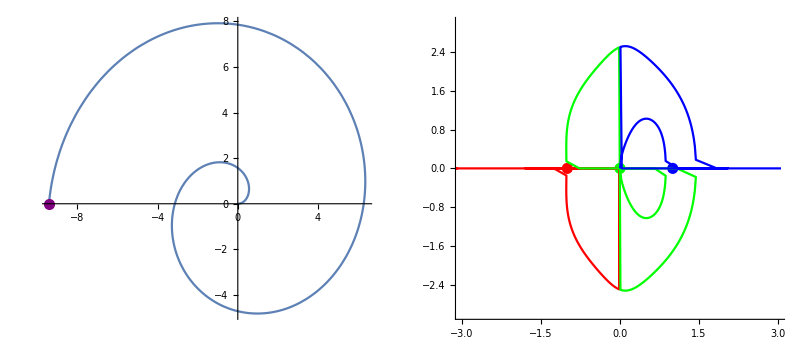

```mathematica
Dance[3π,0,3π,arcx,arcy]
```

```mathematica
archiframes = Table[Dance[t,0,3π,arcx,arcy],{t,0,3π,0.05}];
```

```mathematica
Export["archimedance.gif",archiframes,ImageSize->Large]
```

#### Spirale logaritmica (β=1,κ=-1):

```mathematica
logx[t_]:= E^-t Cos[t]
logy[t_]:=E^-t Sin[t]
Points[a_,b_]:= PointsRange[a,b,1]
```

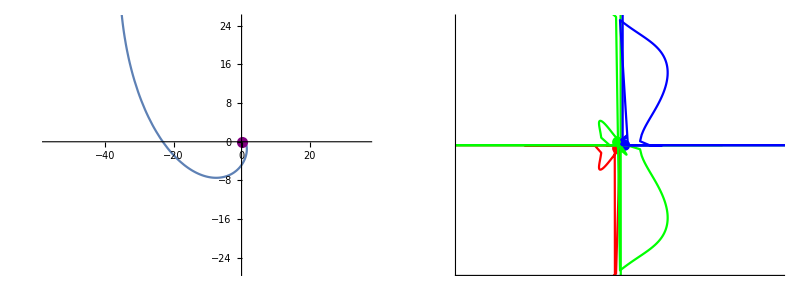

```mathematica
Dance[10,-10,10,logx,logy]
```

```mathematica
logframes = Table[Dance[t,-10,10,logx,logy],{t,-10,10,0.5}];
```

```mathematica
Export["logspirdance.gif",logframes,ImageSize->Large]
```

#### Cardioide:

```mathematica
cardx[t_]:= Cos[t](1+Cos[t])
cardy[t_]:= Sin[t] (1+Cos[t])
Points[a_,b_]:= PointsRange[a,b,1.5]
```

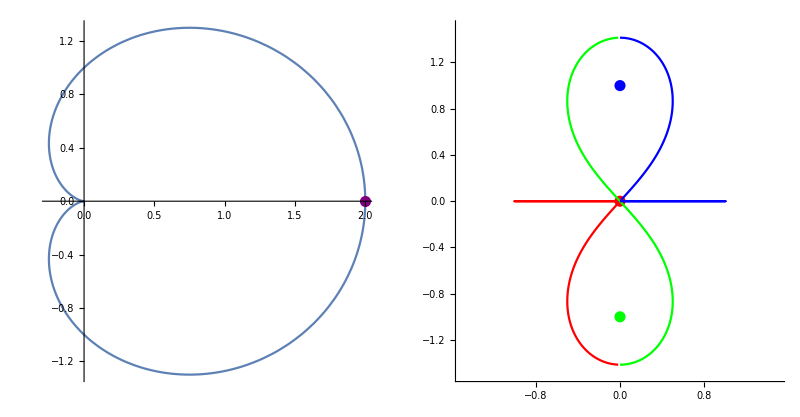

```mathematica
Dance[2π,0,2π,cardx,cardy]
```

```mathematica
cardframes = Table[Dance[t,0,2π,cardx,cardy],{t,0,2π,0.05}];
```

```mathematica
Export["carddance.gif",cardframes,ImageSize->Large]
```

#### Lemniscata di Bernoulli:

```mathematica
lemx[t_]:= Sin[t]/(1+Cos[t]^2)
lemy[t_]:=(Sin[t]Cos[t])/(1+Cos[t]^2)
Points[a_,b_]:= PointsRange[a,b,1.2]
```

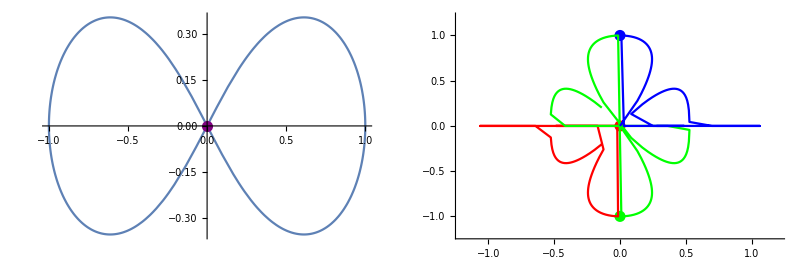

```mathematica
Dance[2π,0,2π,lemx,lemy]
```

```mathematica
lemnframes = Table[Dance[t,0,2π,lemx,lemy],{t,0,2π,0.05}];
```

```mathematica
Export["lemnidance.gif",lemnframes,ImageSize->Large]
```

#### (pezzo di) Folium di Cartesio:

```mathematica
folx[t_]:= t(t-1)
foly[t_]:=t (t-1)(2t-1)
Points[a_,b_]:= PointsRange[a,b,1]
```

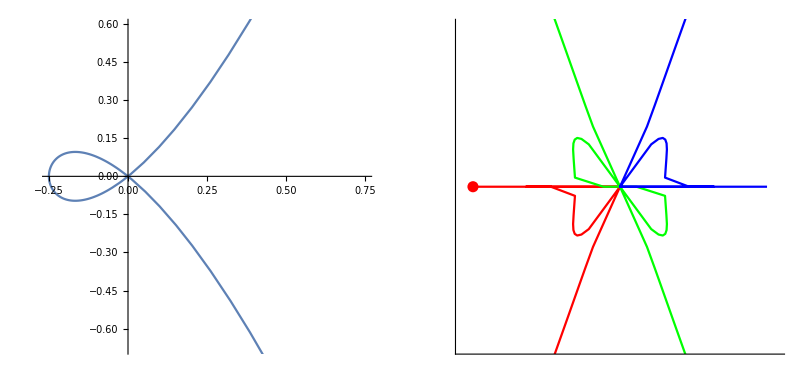

```mathematica
Dance[1.5,-0.5,1.5,folx,foly]
```

```mathematica
foliumframes = Table[Dance[t,-0.5,1.5,folx,foly],{t,-0.5,1.5,0.05}];
```

```mathematica
Export["foliumdance.gif",foliumframes,ImageSize->Large]
```

### Media 3D:

Messa a punto la funzione in 3D lascio immagini e comandi come sopra per alcune curve 3D famose

#### (pezzo di) Nodo di LissaJous (a,b,c,ϕ,ψ,n=1,m=2):

```mathematica
lisx[t_]:= Sin[t]
lisy[t_]:= Sin[t+1]
lisz[t_]:= Sin[2t+1]
Points[a_,b_,c_]:= PointsRange[a,b,c,1.5]
```

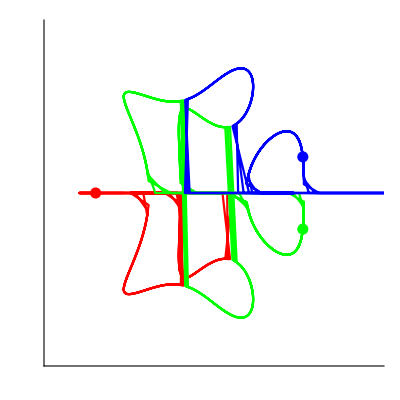

```mathematica
Dance3D[10,-10,10,lisx,lisy,lisz]
```

```mathematica
Lissaframes = Table[Dance3D[t,-10,10,lisx,lisy,lisz],{t,-10,10,0.5}];
```

```mathematica
Export["Lissadance.gif",Lissaframes,ImageSize->Large]
```

#### Bordo della finestra di Viviani:

```mathematica
vivx[t_]:= 1+Cos[t]
vivy[t_]:= Sin[t]
vivz[t_]:= 2Sin[t/2]
Points[a_,b_,c_]:= PointsRange[a,b,c,1.5]
```

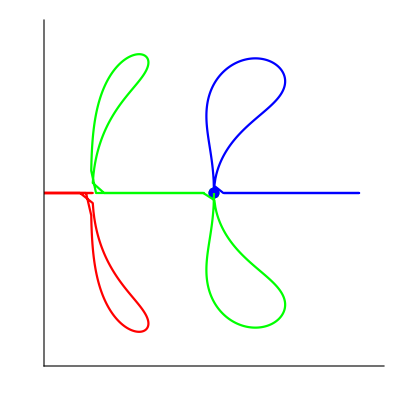

```mathematica
Dance3D[4π,0,4π,vivx,vivy,vivz]
```

```mathematica
Vivianframes = Table[Dance3D[t,0,4π,vivx,vivy,vivz],{t,0,4π,0.1}];
```

```mathematica
Export["Viviandance.gif",Vivianframes,ImageSize->Large]
```

#### Cucitura di una palla da tennis (a,b,c=1):

```mathematica
tenx[t_]:= Cos[t]+Cos[3t]
teny[t_]:= Sin[t]-Sin[3t]
tenz[t_]:= Sin[2t]
Points[a_,b_,c_]:= PointsRange[a,b,c,1.5]
```

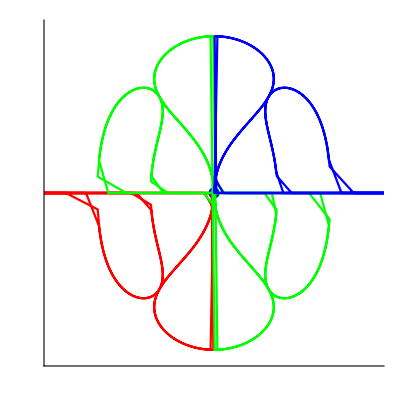

```mathematica
Dance3D[4π,0,4π,tenx,teny,tenz]
```

```mathematica
tennisframes = Table[Dance3D[t,0,4π,tenx,teny,tenz],{t,0,4π,0.1}];
```

```mathematica
Export["tennisdance.gif",tennisframes,ImageSize->Large]
```

### Extra 2 (Cardioidi e Lemniscate):

Il fatto che la cardioide producesse qualcosa di simile alla lemniscata mi ha incuriosito; 
riportiamo la parametrizzazione.

```mathematica
cardx[t_]:= Cos[t](1+Cos[t])
cardy[t_]:= Sin[t] (1+Cos[t])
Points[a_,b_]:= PointsRange[a,b,1.5]
```

Creiamo il grafico solo della parte che ci interessa

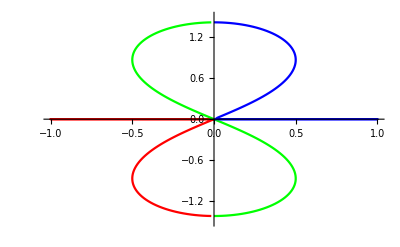

```mathematica
lemnimaybe =Show[{ListLinePlot[Table[C2R2[cardx[τ],cardy[τ],1],{τ,0,2π,0.05}],PlotStyle->Red,PlotRange->{{-1,1},{-1.5,1.5}}],
			ListLinePlot[Table[C2R2[cardx[τ],cardy[τ],2],{τ,0,2π,0.05}],PlotStyle->Green,PlotRange->{{-1,1},{-1.5,1.5}}],
			ListLinePlot[Table[C2R2[cardx[τ],cardy[τ],3],{τ,0,2π,0.05}],PlotStyle->Blue,PlotRange->{{-1,1},{-1.5,1.5}}]}]
```

Cerco di capire quale sia la scala della figura (dove stanno i massimi ed i minimi), posso cercare il massimo delle due coordinate dell punto verde al variare di t

```mathematica
Max[Table[C2R2[cardx[τ],cardy[τ],2][[1]],{τ,0,2π,0.01}]]
Max[Table[C2R2[cardx[τ],cardy[τ],2][[2]],{τ,0,2π,0.01}]]
```

0.5

1.41421

Congetturo che La scala sia di 1/2 nella direzione dell’asse x e di √2nella direzione dell’asse y

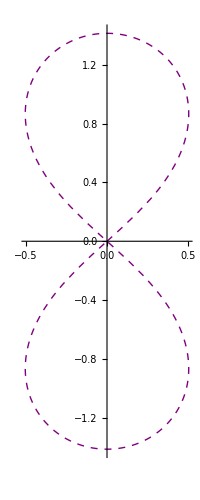

```mathematica
Lemn = ParametricPlot[{1/2(1+Cos[1]^2)/(Cos[1]Sin[1])(Sin[t]Cos[t])/(1+Cos[t]^2),√2 Sin[t]/(1+Cos[t]^2)},{t,0,2π},PlotStyle->{Purple,Dashed,Thick}]
```

```mathematica
Max[Table[(Sin[t]Cos[t])/(1+Cos[t]^2),{t,0,2π}]]
```

(Cos[1] Sin[1])/(1+Cos[1]^2)

Scalo opportunamente la lemniscata e
controlliamo se si sovrappongono

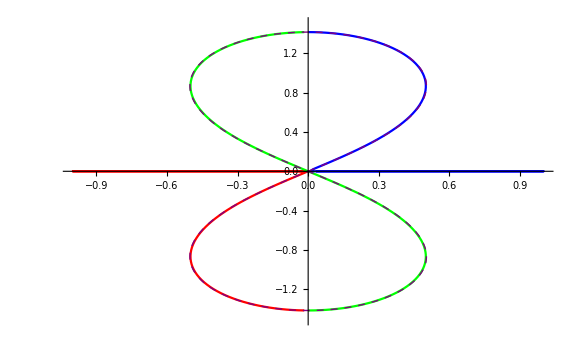

```mathematica
Show[{lemnimaybe,Lemn},ImageSize-> Large]
```

Sembrano sovrapporsi, cercherò di dimostrare questo fatto:
Vogliamo dimostrare che Supp (ℒ) ⊆ (∪^3)_(k=1)Supp(x_k(t)) ,dove ℒ è la Lemniscata di Bernoulli opportunamente scalata e x_1 x_2 e x_3 sono le 3 radici di x^3+a(t)x+b(t), dove a(t)e b(t) variano sulla cardioide

Questo è verificato solo se, posto z(t*)=lemnx(t*)+ 𝒾 lemny(t*)
z(t^*)^3+a(t)z(t^*)+b(t) == 0 ha soluzione ∀t*∈[0,2π] ∃ t ∈[0,2π]

```mathematica
Pcard[t_,x_]:= Norm[P[Cos[t](1+Cos[t]),Sin[t] (1+Cos[t]),x]]
```

```mathematica
cmplxL[t_]:= 1/2(1+Cos[1]^2)/(Cos[1]Sin[1])(Sin[t]Cos[t])/(1+Cos[t]^2)+ I √2 Sin[t]/(1+Cos[t]^2)
```

```mathematica
Manipulate[Plot[Pcard[t,cmplxL[τ]],{t,0,2π},PlotRange->{0,1.5}],{τ,0,2π}]
```

Facendo variare τ si ha che ogni funzione generata ha almeno uno 0 (con le dovute approssimazioni dovute alla limitata precisione delle funzioni e all’approssimazione “a occhio” della parametrizzazione della lemniscata modificata)

La prova non è rigorosa nè particolarmente elegante, tuttavia permette di congetturare la correttezza di un risultato simile (ossia riscalando più accuratamente la lemniscata)

## Esercizio 1.3 (Teorema dei numeri primi).

#### Testo dell’esercizio:

Il teorema dei numeri primi afferma che le funzioni    π(n)   ,   n/log(n)  ,   li(n)   sono asintotiche per   n→∞ .
Investigare numericamente questa affermazione.

### Svolgimento:

## Esercizio 1.4 (Catenaria).

### Testo dell’esercizio:

Se, nel piano xy, un cerchio di raggio r rotola senza strisciare sull’asse x, un punto P del cerchio descrive, nel piano xy, una curva chiamata catenaria, di equazioni parametriche
   t → (rt - r sin(t) , r - r cos(t) )
Produrre un’animazione (e magari un filmato) che mostra il cerchio (o un disco) che  rotola, il punto P su di essa, e la curva descritta da P nel piano

### Svolgimento: